```mathematica
A=2.0; phi=0
```

0

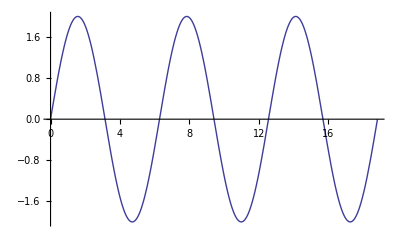

```mathematica
Plot[A*Sin[t+phi],{t,0,6Pi}]
```

```mathematica
freq= 1/(2*Pi)
```

1/(2 π)

```mathematica
N[%]
```

0.159155

```mathematica
ω = 2*Pi*freq
```

1

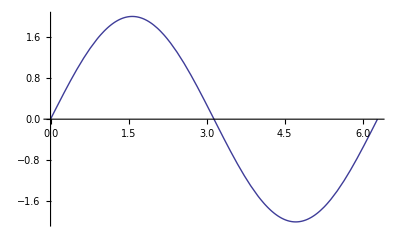

```mathematica
Wave =Plot[A*Sin[ω*t+phi],{t,0,2*Pi}]
```

```mathematica
(*  Right Arrow = Esc  - > Esc  *)
```

```mathematica
Animate[Plot[A*Sin[ω*t+phi],{t,0,2*Pi}],{ω,0,10},{phi,0,2 π},AnimationRunning ->False]
```

```mathematica
y[x,t]= A*Sin[(2*Pi/λ)*(x-Velocity*t)]
```

2. Sin[5000000 π (-4.×10^8 t+x)]

```mathematica
Velocity=2; λ= 3.0;
```

```mathematica
Plot3D[ Sin[(2*Pi/λ)*(x-Velocity*t)],{x,0,6},{t,0,7}]
```

-Graphics3D-

```mathematica
(*  Let' s select light with velocity = c and a wavelength of 400 nm  *)
```

```mathematica
Velocity = 4.0*10^8
```

4.×10^8

```mathematica
λ= 400*10^-9
```

1/2500000

```mathematica
Plot3D[ Sin[(2*Pi/λ)*(x-Velocity*t)],{x,0,2*λ},{t,0,2*λ/Velocity}]
```

-Graphics3D-

```mathematica
λ/Velocity
```

1.×10^-15